```mathematica
ClearAll;
SetDirectory[NotebookDirectory[]];
strm=OpenWrite["output.log"];
$Output={strm};

SetOptions[EvaluationNotebook[],CellEvaluationFunction->(ToExpression[#,StandardForm,Function[Null,Module[{aborted=$Aborted},Internal`WithLocalSettings[Null,aborted=(ReleaseHold[Most[Hold[##]]];Last[Hold[##]]),AbortProtect[If[aborted===$Aborted,Print["Did cleanup"];Abort[]]]]],HoldAll]]&)];
```

```mathematica
(*Needs["IGraphM`"]*)

(*g=IGWeightedAdjacencyGraph[capturedFromPSO]*)
<<IGraphM``
```

IGraph/M 0.6.5 (December 21, 2022)
Evaluate IGDocumentation[] to get started.

```mathematica
(*Schwefel' s Function*)
fun4Name="Schwefel' s Function";
fun4[x_]:=Module[{l=Length@x}, Sum[-x[[i]] Sin[Sqrt[Abs[x[[i]]]]], {i,l}]];
Plot[fun4@{x},{x,-420.969,420.969}]
Plot3D[fun4@{x1,x2},{x1,-420.969,420.969},{x2,-420.969,420.969}]
```

-Graphics3D-

```mathematica
draw[matrix_]:=Module[{f,g,adjacencyMatrix,vertices},
adjacencyMatrix=matrix;
adjacencyMatrix=Rescale@adjacencyMatrix/. 0->∞//N;
f[pts_List,e_]:=Block[
{s=0.015,weight=PropertyValue[{g,e},EdgeWeight]},
{
ColorData["TemperatureMap"][weight],
Arrowheads[{{s,0.1},{s,0.9}}],
AbsoluteThickness[weight*15],
Arrow[pts]
}
];

vertices=Join[{{0,0}},Table[{4 Cos[a],4 Sin[a]},{a,Pi/4,2 Pi,Pi/4}],Table[{7 Cos[a],7 Sin[a]},{a,0,5 Pi/3,Pi/6}]][[1;;Length@adjacencyMatrix]];
g=WeightedAdjacencyGraph[adjacencyMatrix,
VertexLabels->"Name",
EdgeLabels->(*"EdgeWeight"*)None,
EdgeShapeFunction->f,
VertexLabelStyle->Directive[Black,Bold,20],
ImageSize->Large,
Background->GrayLevel@0.8,
VertexCoordinates->vertices
(*,
VertexCoordinates->vertices*)
];
Return@g;
];
```

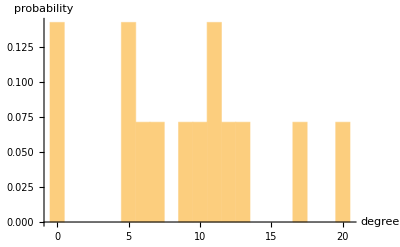

```mathematica
realData={
	{18,5,2,  4 ,   9,  0,  0,  5, 0, 3,   1,   5,    0,   0},
	{  3,6,0,  2 ,   2,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  1,3,3,  4 ,   3,  0,  0,  0, 0, 0,   0,   1,   0,    0},
	{  9,0,0, 68,  25,  0,  0,  0, 0, 6,  12,   0,   6,    0},
	{19,4,1,57, 139,  0,  0, 0, 0, 7,  62,  0,  44,  0},
	{  1,0,0,  0 ,   0,  5,  4,  0, 0,  0,   0,    0,   0,   0},
	{  1,0,0,  0 ,   0,  3,  2,  0, 0,  0,   0,    0,   0,   0},
	{  6,0,0,  0 ,   1,  0,  0,  2, 0,  0,   0,    3,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  0,0,0,  0 ,   0,  0,  0,  0, 0,  0,   0,    0,   0,   0},
	{  8,2,0,44 , 85, 0,  0,  0, 0,  4,  53,   0,  35,  0},
	{  8,1,0,  0 ,   1,  1,  0,  2, 0,  0,   0,    6,   0,   0},
	{  1,0,0, 25 , 59,  0,  0, 0, 0,  1,  47,   0,  37,  0},
	{  0,0,0,  0 ,   0,   0,  0,  0, 0,  0,    0,    0,   0,   0} };
realData=realData[[All,1;;Length@realData]];
g1=draw@realData
Histogram[VertexDegree[g1],{1},"Probability",AxesLabel->{"degree","probability"}]
```

```mathematica
pts[m_,r_]:=Module[{pts,DCr, DCm, CCr,CCm,BCm, BCr, EVCr, EVCm, ICr, ICm},
pts=0;

DCm = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@m];
DCr = Mean[DegreeCentrality@IGWeightedAdjacencyGraph@r];

CCm=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@m];
CCr=Mean[ClosenessCentrality@IGWeightedAdjacencyGraph@r];

BCm=Mean[IGBetweenness@IGWeightedAdjacencyGraph@m];
BCr=Mean[IGBetweenness@IGWeightedAdjacencyGraph@r];

EVCm=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@m];
EVCr=Mean[IGEigenvectorCentrality@WeightedAdjacencyGraph@r];
(*Information centrality*)
pts=((DCr-DCm)/DCr)^2+((CCr-CCm)/CCr)^2+((BCr-BCm)/BCr)^2+((EVCr-EVCm)/EVCr)^2;
pts*=1000;
Return@pts
];
```

```mathematica
calculateFitness[f_,fLimit_,swarmDim_,
 NPForInnerPSO_,c1_, c2_, w_,  iterationsForInnerPSO_, swarmPositionForInnerPSO_, realData_, pts_]:=Module[
{communicationList, capturedDataFromPSO, sortedCapturedDataFromPSO,
matrixFormSortedCapturedDataFromPSO, testList, capturedFromPSO,
subList,particlePositionCost,
m,p},
communicationList = PSOAlgorithmInner[f,fLimit,swarmDim,NPForInnerPSO,c1,c2,w, iterationsForInnerPSO, swarmPositionForInnerPSO];
(*Print["Output from inner PSO inside loop = ",communicationList];*)
capturedDataFromPSO=communicationList;
sortedCapturedDataFromPSO = Sort[capturedDataFromPSO,#1[[1]]<#2[[1]]&];
(*Print["sorted communicationList inside loop= ",sortedCapturedDataFromPSO];*)
matrixFormSortedCapturedDataFromPSO = AdjacencyMatrix@capturedDataFromPSO //MatrixForm;
testList=AdjacencyMatrix@sortedCapturedDataFromPSO;
(*Print["testList communicationList inside loop= ",testList];*)
capturedFromPSO={};
For[m=1,m<=Length@testList,m++,
subList={};
For[p=1,p<=Length@testList,p++,
AppendTo[subList, testList[[m]][[p]]];
];
AppendTo[capturedFromPSO, subList];
];
capturedFromPSO=capturedFromPSO[[All,1;;Length@capturedFromPSO]];
(*Print["capturedfrom PSO inside loop= ",capturedFromPSO];*)
particlePositionCost =pts[capturedFromPSO,realData];
Return@particlePositionCost;
];
```

```mathematica
PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_, swarmPositionFromOuterPSO_
]:=Module[
{
inertia,swarmPosition,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,gBestPosition,gBestPositionIndex,
gBestCost,FitnessFunction,fLowerBound,fUpperBound,f1,
rand1,
rand2,
i,j,n,
historyGBestPosition,historyGBestCost,communicationList,
it
},

inertia=ConstantArray[0,{NP,swarmDim}];
swarmPosition=swarmPositionFromOuterPSO;
swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=ConstantArray[0,{NP,swarmDim}];
pBestCost=Table[0,NP];
swarmPositionCost=Table[0,NP];
gBestPosition=Table[0,swarmDim];
gBestCost=0;
gBestPositionIndex;
FitnessFunction=f;
f1=FitnessFunction;
fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];
historyGBestPosition={};
historyGBestCost={};
communicationList={};

swarmVelocity=ConstantArray[0,{NP,swarmDim}];
pBestPosition=swarmPosition;
f1[x__]:=Re[Map[FitnessFunction,{x}]];

swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];
gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
gBestPositionIndex=First@First@Position[swarmPositionCost,gBestCost];

For[j=1,j<=Length@swarmPosition,j++,
If[j== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, gBestPositionIndex <-> j];
];
(*Main Loop*)

it=0;
While[it< iterations,
{

(*Update the velocity and position vectors*)
For[i=1,i≤  (NP),i++,
For[j=1,j≤  (swarmDim),j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
For[j=1,j<=swarmDim,j++,
If[swarmPosition[[i,j]]<fLowerBound,swarmPosition[[i,j]]=RandomReal@fLimit];
If[swarmPosition[[i,j]]>fUpperBound,swarmPosition[[i,j]]=RandomReal@fLimit];
];
n=0;
f1[x__]:=Map[FitnessFunction,{x}];
swarmPositionCost=Table[f1[swarmPosition[[n]]],{n,NP}];

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];
If[pBestCost[[i]]<= gBestCost,
{

AppendTo[communicationList,First@First@Position[swarmPosition, pBestPosition[[i]] ]<-> gBestPositionIndex]; 
For[j=1,j<=Length@swarmPosition,j++,
If[j== gBestPositionIndex, Continue[]];(*This is to avoid double connection between gBest and current particle position*)
	AppendTo[communicationList, i <-> j];
];
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];
gBestPositionIndex=First@First@Position[swarmPosition, pBestPosition[[i]] ];
};
];
}
];
];
AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];
,it++
}
];
Return@communicationList;
];
```

```mathematica
PSOAlgorithmOuter[ f_,swarmDimInnerPSO_,fLimit_,(*just for inner*)
 NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_,
 c1_, c2_, w_, realData_, pts_, calculateFitness_,swarmDimOuterPSO_,c1Limit_,c2Limit_,wLimit_,lusSearchIterations_(*just for outer*)
]:=Module[
{
inertia,swarmPosition,swarmVelocity,pBestPosition,
pBestCost,swarmPositionCost,gBestPosition,
gBestCost,fLowerBound,fUpperBound,
rand1,
rand2,
i,j,
historyGBestPosition,historyGBestCost,
it, particlePositionCost,
c1Parameter, c2Parameter, wParametere ,
c1LowerLimit,
c1UpperLimit, c2LowerLimit,c2UpperLimit,
wLowerLimit, wUpperLimit,
 swarmPositionForInnerPSO,
sigma, lucRadius, lBestPosition, lBestFitness, candidatePositionLus,candidateFitnessLus,
predictionDataList
},
lBestPosition=Table[0,swarmDimOuterPSO];
lBestFitness=0.0;
sigma = 0;
lucRadius=0;
fLowerBound=fLimit[[1]];
fUpperBound=fLimit[[2]];
swarmPositionForInnerPSO=RandomReal[{fLowerBound,fUpperBound},{NPForInnerPSO,swarmDimInnerPSO}];
inertia=ConstantArray[0,{NPForOuterPSO,swarmDimOuterPSO}];
swarmPosition=ConstantArray[0,{NPForOuterPSO,swarmDimOuterPSO}];
swarmVelocity=ConstantArray[0,{NPForOuterPSO,swarmDimOuterPSO}];
pBestPosition=ConstantArray[0,{NPForOuterPSO,swarmDimOuterPSO}];
pBestCost=Table[0,NPForOuterPSO];
swarmPositionCost=Table[0,NPForOuterPSO];
gBestPosition=Table[0,swarmDimOuterPSO];
historyGBestPosition={};
historyGBestCost={};
c1LowerLimit=c1Limit[[1]];
c1UpperLimit=c1Limit[[2]];
c1Parameter = RandomReal[{c1LowerLimit,c1UpperLimit},{NPForOuterPSO,1}];
c1Parameter=Flatten@c1Parameter;

c2LowerLimit=c2Limit[[1]];
c2UpperLimit=c2Limit[[2]];
c2Parameter = RandomReal[{c2LowerLimit,c2UpperLimit},{NPForOuterPSO,1}];
c2Parameter=Flatten@c2Parameter;

wLowerLimit=wLimit[[1]];
wUpperLimit=wLimit[[2]];
wParametere = RandomReal[{wLowerLimit,wUpperLimit},{NPForOuterPSO,1}];
wParametere=Flatten@wParametere;
particlePositionCost=0;

(*predictionDataList=ConstantArray[0,{iterationsForOuterPSO,4}];*)
predictionDataList={};

For[j=1,j<=NPForOuterPSO,j++,
swarmPosition[[j]]={c1Parameter[[j]], c2Parameter[[j]],wParametere[[j]]};
];
Print["Initial outerPSO population", swarmPosition];
pBestPosition=swarmPosition;

For[j=1,j<= NPForOuterPSO, j++,
particlePositionCost = calculateFitness[f,fLimit ,swarmDimInnerPSO,NPForInnerPSO,swarmPosition[[j]][[1]],swarmPosition[[j]][[2]],swarmPosition[[j]][[3]], iterationsForInnerPSO, swarmPositionForInnerPSO,realData, pts];
swarmPositionCost[[j]]= particlePositionCost;
];
Print["Initial outerPSO population cost (pBest)", swarmPositionCost];
pBestCost=swarmPositionCost;
gBestCost=Min[pBestCost];

gBestPosition=pBestPosition[[First@First@Position[swarmPositionCost,gBestCost]]];
Print["Initial outerPSO gBest position", gBestPosition];
Print["Initial outerPSO gBest cost", gBestCost];

it=0;
While[it< iterationsForOuterPSO,
{
Print["OuterPSO iteration number it = ", it];
For[i=1,i≤  (NPForOuterPSO),i++,
(*calculate standard deviation sigma of distances between the particle and the global best position in each dimension*)
(*sigma=StandardDeviation[gBestPosition-swarmPosition[[i]]];
lucRadius = sigma;
(*Print["standard deviation sigma is ", lucRadius];*)
lBestPosition=swarmPosition[[i]];
lBestFitness = calculateFitness[f,fLimit,swarmDimInnerPSO,NPForInnerPSO,swarmPosition[[i]][[1]],swarmPosition[[i]][[2]],swarmPosition[[i]][[3]], iterationsForInnerPSO, swarmPositionForInnerPSO, realData, pts];
Print["Fitness of particle in outerPSO at position = ",i,lBestFitness ];
(*Print["Fitness for initial position for local search ", lBestFitness];*)

For[j=1,j<=lusSearchIterations,j++,
candidatePositionLus = swarmPosition[[i]] + lucRadius * RandomVariate[NormalDistribution[0,1],Dimensions[swarmPosition[[i]]]];*)
(*Print["Candidate position for local search ", candidatePositionLus];*)
(*If[candidatePositionLus[[1]] >c1LowerLimit  &&  candidatePositionLus[[1]]<c1UpperLimit  && 
candidatePositionLus[[2]] >c2LowerLimit  && candidatePositionLus[[2]] <c2UpperLimit  &&
candidatePositionLus[[3]] >wLowerLimit  && candidatePositionLus[[3]] <wUpperLimit,

    candidateFitnessLus = calculateFitness[f,fLimit,swarmDimInnerPSO,NPForInnerPSO,candidatePositionLus[[1]],candidatePositionLus[[2]],candidatePositionLus[[3]], iterationsForInnerPSO, swarmPositionForInnerPSO,  realData, pts];
Print["Candidate position for local search is within the boundary and its fitness is ", candidateFitnessLus];
If[candidateFitnessLus <  lBestFitness,
	lBestFitness = candidateFitnessLus;
	(*swarmPositionCost=lBestFitness;*)
	lBestPosition = candidatePositionLus;
	(*swarmPosition[[i]]=lBestPosition;*)
];
];
];*)

For[j=1,j≤  swarmDimOuterPSO,j++,
rand1=RandomReal[{0,1}];
rand2=RandomReal[{0,1}];
inertia=w*swarmVelocity[[i]][[j]];
swarmVelocity[[i]]= inertia + (c1 * rand1 * (pBestPosition[[i]][[j]]- swarmPosition[[i]][[j]]))+
(c2 *rand2 * (gBestPosition - swarmPosition[[i]][[j]]));
];

(*Update the particle's position*)
swarmPosition[[i]] +=swarmVelocity[[i]];
(*Print["Swarm position being updated",swarmPosition];*)
For[j=1,j<=NPForOuterPSO,j++,
If[swarmPosition[[i,1]]<c1LowerLimit,swarmPosition[[i,1]]=RandomReal@c1Limit];
If[swarmPosition[[i,1]]>c1UpperLimit,swarmPosition[[i,1]]=RandomReal@c1Limit];

If[swarmPosition[[i,2]]<c2LowerLimit,swarmPosition[[i,2]]=RandomReal@c2Limit];
If[swarmPosition[[i,2]]>c2UpperLimit,swarmPosition[[i,2]]=RandomReal@c2Limit];

If[swarmPosition[[i,3]]<wLowerLimit,swarmPosition[[i,3]]=RandomReal@wLimit];
If[swarmPosition[[i,3]]>wUpperLimit,swarmPosition[[i,3]]=RandomReal@wLimit];
];
(*n=0;*)

(*PSOAlgorithmInner[f_, fLimit_, swarmDim_, NP_, c1_, c2_, w_, iterations_*)
particlePositionCost = calculateFitness[f,fLimit,swarmDimInnerPSO,NPForInnerPSO,swarmPosition[[i]][[1]],swarmPosition[[i]][[2]],swarmPosition[[i]][[3]], iterationsForInnerPSO, swarmPositionForInnerPSO, realData, pts];
(*Print["Output from inner PSO inside loop = ",communicationList];*)

AppendTo[predictionDataList, {swarmPosition[[i]][[1]], swarmPosition[[i]][[2]], swarmPosition[[i]][[3]], particlePositionCost}];

swarmPositionCost[[i]] =particlePositionCost;

(*Update pBest and gBest*)
If[swarmPositionCost[[i]]<= pBestCost[[i]],
{
pBestCost[[i]]=swarmPositionCost[[i]];
pBestPosition[[i]]=swarmPosition[[i]];

If[pBestCost[[i]]<= gBestCost,
{
(*Print@"----Particle updating the gBest From OUter-------";*)
gBestCost=pBestCost[[i]];
gBestPosition=pBestPosition[[i]];

};
];
}
];


];

AppendTo[historyGBestPosition,gBestPosition];
AppendTo[historyGBestCost,gBestCost];

,it++
}];
Return@{gBestPosition,gBestCost, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition, predictionDataList};
];
```

```mathematica
functionUsed=fun4;
swarmDimensionForInnerPSO = 5;
swarmDimensionForOuterPSO = 3; (*Always 3*)
functionLimits={-5,5};
NPForInnerPSO=14;
NPForOuterPSO=30;
iterationsForInnerPSO=50;
iterationsForOuterPSO=1000;
C1ParameterForOuterPSO=1.49445;
c1LimitForOuterPSOPopulation={1.0,2.0};
C2ParameterForOuterPSO=1.49445;
c2LimitForOuterPSOPopulation={1.0,2.0};
WParameterForOuterPSO=0.729;
wLimitForOuterPSOPopulation={0.4,0.9};
lusSearchIterations=50;

Print["Function used for inner PSO  is ",fun4Name];
Print["Swarm dimensions of Inner PSO is ", swarmDimensionForInnerPSO];
Print["Swarm dimensions of Outer PSO is ", swarmDimensionForOuterPSO];
Print["Function range is ", functionLimits];
Print["Population size for inner PSO is ", NPForInnerPSO];
Print["Population size for outer PSO is ", NPForOuterPSO];
Print["Max Iterations for inner PSO is ", iterationsForInnerPSO];
Print["Max Iterations for outer PSO is ", iterationsForOuterPSO];
Print["C1 parameter for outer PSO is ", C1ParameterForOuterPSO];
Print["C1 population limit for outer PSO is ", c1LimitForOuterPSOPopulation];
Print["C2 parameter for outer PSO is ", C2ParameterForOuterPSO];
Print["C2 population limit for outer PSO is ", c2LimitForOuterPSOPopulation];
Print["W parameter for outer PSO is ", WParameterForOuterPSO];
Print["W population limit for outer PSO is ", wLimitForOuterPSOPopulation];
Print["Number of iterations for local search (LUS) is ", lusSearchIterations];
(*PSOAlgorithmOuter[ f_,swarmDimInnerPSO_,fLimit_,(*just for inner*)
 NPForInnerPSO_,NPForOuterPSO_,  iterationsForInnerPSO_,iterationsForOuterPSO_,
 c1_, c2_, w_, realData_, pts_, calculateFitness_,swarmDimOuterPSO_,c1Limit_,c2Limit_,wLimit_,lusSearchIterations_(*just for outer*)]
]*)
outputFromOuterPSO = PSOAlgorithmOuter[functionUsed, swarmDimensionForInnerPSO,functionLimits, NPForInnerPSO,NPForOuterPSO,iterationsForInnerPSO,iterationsForOuterPSO,C1ParameterForOuterPSO,C2ParameterForOuterPSO, WParameterForOuterPSO,  realData, pts, calculateFitness,swarmDimensionForOuterPSO,c1LimitForOuterPSOPopulation,c2LimitForOuterPSOPopulation,wLimitForOuterPSOPopulation, lusSearchIterations];
```

```mathematica
(*Return@{gBestPosition,gBestCost, historyGBestPosition, historyGBestCost,swarmPositionCost, swarmPosition};*)
```

```mathematica
Print["Complete output from outer PSO : ",outputFromOuterPSO];
```

```mathematica
Print["History of best pts value (gBestCost history) : ", outputFromOuterPSO[[4]]];
```

```mathematica
Print["Pts values at all positions(pBestCost) : ", outputFromOuterPSO[[5]]];
```

```mathematica
Print["Minimum value of pts detected (gBestCost) : ", outputFromOuterPSO[[2]]];
```

```mathematica
Print["all parameters position (swarm position) : ", allParametersPosition =outputFromOuterPSO[[6]]];
```

```mathematica
Print["Parameters for minimun values of pts (gBestPosition) : ", outputFromOuterPSO[[1]]];
Print["Prediction data list : ", outputFromOuterPSO[[7]]];

(*code for prediction start*)
dataForPrediction = outputFromOuterPSO[[7]];
dataForPrediction=RandomSample[dataForPrediction];
trainingSet=Take[dataForPrediction,Round[0.8*Length[dataForPrediction]]];
testSet=Take[dataForPrediction,{Round[0.8*Length[dataForPrediction]]+1,Length[dataForPrediction]}];

lm=LinearModelFit[trainingSet,{x1,x2,x3},{x1,x2,x3}];

testPredictions=lm[Sequence@@#]&/@testSet[[All,1;;-2]];

mae=Mean[Abs[testPredictions-testSet[[All,-1]]]];
rmse=Sqrt[Mean[(testPredictions-testSet[[All,-1]])^2]];

Print["MAE: ",mae]
Print["RMSE: ",rmse]

(*code for prediction end*)
```

```mathematica
lm
```

lm

```mathematica
Close[strm];
```